```mathematica
ClearAll["Global`*"]
```

```mathematica
T12t1 = 7;
T12t2 = 8;
T12ct1 = 8;
T12ct2 = 9;
T12n = 5;

T12[t_, s_,i_,r_]:=If[ Mod[t,24] ≥ T12t1 && Mod[t,24] ≤ T12t2, T12n/(T12t2-T12t1)1/(s+i+r),0]
cT12[t_, s_,i_,r_]:=If[ Mod[t,24] ≥ T12ct1 && Mod[t,24]≤ T12ct2, T12n/(T12ct2-T12ct1)1/(s+i+r),0]

T21t1 = 18;
T21t2 = 19;
T21ct1 = 19;
T21ct2 = 20;
T21n = 5;

T21[t_, s_,i_,r_]:=If[ Mod[t,24] ≥ T21t1 && Mod[t,24] ≤ T21t2, T21n/(T21t2-T21t1)1/(s+i+r),0]
cT21[t_, s_,i_,r_]:=If[ Mod[t,24]≥ T21ct1 && Mod[t,24] ≤ T21ct2, T21n/(T21ct2-T21ct1)1/(s+i+r),0]
λ[t_,s_,i_,r_]:= If[i≠ 0, (β i)/(s+i+r),0]
```

```mathematica
β=0.0002*60;
γ=0.00005*60;
tstart = 0;
tend = 24;
```

```mathematica
sol = NDSolve[{
s1'[t]== -λ[t,s1[t],i1[t],r1[t]] s1[t] 
-s1[t]T12[t, s1[t],i1[t],r1[t]]
+sc21[t]cT21[t,sc21[t],ic21[t],rc21[t]],
i1'[t]==  λ[t,s1[t],i1[t],r1[t]]s1[t]-γ i1[t]
-i1[t]T12[t, s1[t],i1[t],r1[t]]
+ic21[t]cT21[t,sc21[t],ic21[t],rc21[t]],
r1'[t]== γ i1[t]
-r1[t]T12[t, s1[t],i1[t],r1[t]]
+rc21[t]cT21[t,sc21[t],ic21[t],rc21[t]],

sc12'[t]== - λ[t,sc12[t],ic12[t],rc12[t]] sc12[t] 
-sc12[t]cT12[t,sc12[t],ic12[t],rc12[t]]
+s1[t]T12[t, s1[t],i1[t],r1[t]],
ic12'[t]==  λ[t,sc12[t],ic12[t],rc12[t]]sc12[t]-γ ic12[t]
-ic12[t]cT12[t,sc12[t],ic12[t],rc12[t]]
+i1[t]T12[t, s1[t],i1[t],r1[t]],
rc12'[t]== γ ic12[t]
-rc12[t]cT12[t,sc12[t],ic12[t],rc12[t]]
+r1[t]T12[t, s1[t],i1[t],r1[t]],

s2'[t]== -λ[t,s2[t],i2[t],r2[t]] s2[t] 
-s2[t]T21[t, s2[t],i2[t],r2[t]]
+sc12[t]cT12[t,sc12[t],ic12[t],rc12[t]],
i2'[t]==  λ[t,s2[t],i2[t],r2[t]]s2[t]-γ i2[t]
-i2[t]T21[t, s2[t],i2[t],r2[t]]
+ic12[t]cT12[t,sc12[t],ic12[t],rc12[t]],
r2'[t]== γ i2[t]
-r2[t]T21[t, s2[t],i2[t],r2[t]]
+rc12[t]cT12[t,sc12[t],ic12[t],rc12[t]],

sc21'[t]== - λ[t,sc21[t],ic21[t],rc21[t]] sc21[t] 
-sc21[t]cT21[t,sc21[t],ic21[t],rc21[t]]
+s2[t]T21[t, s2[t],i2[t],r2[t]],
ic21'[t]==  λ[t,sc21[t],ic21[t],rc21[t]]sc21[t]-γ ic21[t]
-ic21[t]cT21[t,sc21[t],ic21[t],rc21[t]]
+i2[t]T21[t, s2[t],i2[t],r2[t]],
rc21'[t]== γ ic21[t]
-rc21[t]cT21[t,sc21[t],ic21[t],rc21[t]]
+r2[t]T21[t, s2[t],i2[t],r2[t]],

s1[0]== 9,
i1[0]== 1,
r1[0]== 0,
s2[0]== 10,
i2[0]== 0,
r2[0]== 0,
sc12[0]== 0,
ic12[0]== 0,
rc12[0]== 0,
sc21[0]== 0,
ic21[0]== 0,
rc21[0]== 0
},{s1[t],r1[t],i1[t],s2[t],r2[t],i2[t],sc12[t],ic12[t],rc12[t],sc21[t],ic21[t],rc21[t]},{t,tstart,tend}][[1]];
```

NDSolve::ndsz: At t == 9.00011, step size is effectively zero; singularity or stiff system suspected.

```mathematica
sols = {s1[t],r1[t],i1[t],s2[t],r2[t],i2[t],sc12[t],ic12[t],rc12[t],sc21[t],ic21[t],rc21[t]}/.sol//Flatten;
```

```mathematica
sol = NDSolve[{
s1'[t]== -λ[t,s1[t],i1[t],r1[t]] s1[t] 
-s1[t]T12[t, s1[t],i1[t],r1[t]]
+sc21[t]cT21[t,sc21[t],ic21[t],rc21[t]],
i1'[t]==  λ[t,s1[t],i1[t],r1[t]]s1[t]-γ i1[t]
-i1[t]T12[t, s1[t],i1[t],r1[t]]
+ic21[t]cT21[t,sc21[t],ic21[t],rc21[t]],
r1'[t]== γ i1[t]
-r1[t]T12[t, s1[t],i1[t],r1[t]]
+rc21[t]cT21[t,sc21[t],ic21[t],rc21[t]],

sc12'[t]== - λ[t,sc12[t],ic12[t],rc12[t]] sc12[t] 
-sc12[t]cT12[t,sc12[t],ic12[t],rc12[t]]
+s1[t]T12[t, s1[t],i1[t],r1[t]],
ic12'[t]==  λ[t,sc12[t],ic12[t],rc12[t]]sc12[t]-γ ic12[t]
-ic12[t]cT12[t,sc12[t],ic12[t],rc12[t]]
+i1[t]T12[t, s1[t],i1[t],r1[t]],
rc12'[t]== γ ic12[t]
-rc12[t]cT12[t,sc12[t],ic12[t],rc12[t]]
+r1[t]T12[t, s1[t],i1[t],r1[t]],

s2'[t]== -λ[t,s2[t],i2[t],r2[t]] s2[t] 
-s2[t]T21[t, s2[t],i2[t],r2[t]]
+sc12[t]cT12[t,sc12[t],ic12[t],rc12[t]],
i2'[t]==  λ[t,s2[t],i2[t],r2[t]]s2[t]-γ i2[t]
-i2[t]T21[t, s2[t],i2[t],r2[t]]
+ic12[t]cT12[t,sc12[t],ic12[t],rc12[t]],
r2'[t]== γ i2[t]
-r2[t]T21[t, s2[t],i2[t],r2[t]]
+rc12[t]cT12[t,sc12[t],ic12[t],rc12[t]],

sc21'[t]== - λ[t,sc21[t],ic21[t],rc21[t]] sc21[t] 
-sc21[t]cT21[t,sc21[t],ic21[t],rc21[t]]
+s2[t]T21[t, s2[t],i2[t],r2[t]],
ic21'[t]==  λ[t,sc21[t],ic21[t],rc21[t]]sc21[t]-γ ic21[t]
-ic21[t]cT21[t,sc21[t],ic21[t],rc21[t]]
+i2[t]T21[t, s2[t],i2[t],r2[t]],
rc21'[t]== γ ic21[t]
-rc21[t]cT21[t,sc21[t],ic21[t],rc21[t]]
+r2[t]T21[t, s2[t],i2[t],r2[t]],


s1[0]== 9,
i1[0]== 1,
r1[0]== 0,
s2[0]== 10,
i2[0]== 0,
r2[0]== 0,
sc12[0]== 0,
ic12[0]== 0,
rc12[0]== 0,
sc21[0]== 0,
ic21[0]== 0,
rc21[0]== 0
},{s1[t],r1[t],i1[t],s2[t],r2[t],i2[t],sc12[t],ic12[t],rc12[t],sc21[t],ic21[t],rc21[t]},{t,tstart,tend},
PrecisionGoal->20][[1]];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NDSolve::nlnum: The function value {0.00818548,Indeterminate,Indeterminate,0.,0.00319182,Indeterminate,Indeterminate,0.,-0.0113773,Indeterminate,Indeterminate,0.} is not a list of numbers with dimensions {12} at {t,i1[t],i2[t],ic12[t],ic21[t],r1[t],r2[t],rc12[t],rc21[t],s1[t],s2[t],sc12[t],sc21[t],NDSolve`s$111905[t],NDSolve`s$111901[t],NDSolve`s$111914[t],NDSolve`s$111899[t],NDSolve`s$111924[t]} = {8.,1.06394,0.,0.,0.,0.0247611,0.,0.,0.,8.9113,10.,0.,0.,1,1,-1,1,1}.

```mathematica
sols = {s1[t]+r1[t]+i1[t]}/.sol//Flatten;
Plot[sols, {t,tstart,24},PlotRange->All]
```

-Graphics-

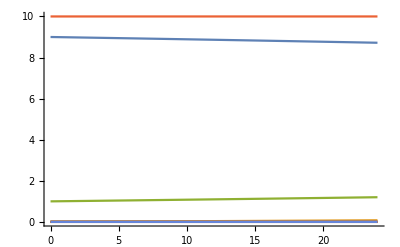

```mathematica
sols = {s1[t],r1[t],i1[t],s2[t],r2[t],i2[t],sc12[t],ic12[t],rc12[t],sc21[t],ic21[t],rc21[t]}/.sol//Flatten;
Plot[sols, {t,tstart,24},PlotRange->All]
```

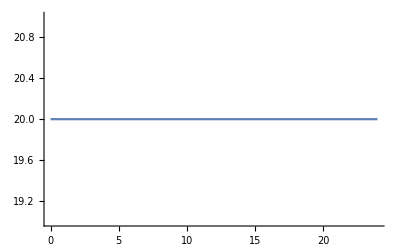

```mathematica
Plot[Total[sols], {t,tstart,tend},PlotRange->All]
```

```mathematica
T12t1 = 7;
T12t2 = 8;
T12ct1 = 8;
T12ct2 = 9;
T12n = 5;

T12[t_, s_,i_,r_]:=If[ Mod[t,24] ≥ T12t1 && Mod[t,24] ≤ T12t2, T12n/(T12t2-T12t1)1/(s+i+r),0]
cT12[t_, s_,i_,r_]:=If[ Mod[t,24] ≥ T12ct1 && Mod[t,24]≤ T12ct2, T12n/(T12ct2-T12ct1)1/(s+i+r),0]

T21t1 = 18;
T21t2 = 19;
T21ct1 = 19;
T21ct2 = 20;
T21n = 5;

T21[t_, s_,i_,r_]:=If[ Mod[t,24] ≥ T21t1 && Mod[t,24] ≤ T21t2, T21n/(T21t2-T21t1)1/(s+i+r),0]
cT21[t_, s_,i_,r_]:=If[ Mod[t,24]≥ T21ct1 && Mod[t,24] ≤ T21ct2, T21n/(T21ct2-T21ct1)1/(s+i+r),0]
λ[t_,s_,i_,r_]:= If[i≠ 0, (β i)/(s+i+r),0]

β=0.0002*60;
γ=0.00005*60;
```

```mathematica
system[t_,{s1_,i1_,r1_,s2_,i2_,r2_,sc12_,ic12_,rc12_,sc21_,ic21_,rc21_}]:={
-λ[t,s1,i1,r1] s1
-s1 T12[t,s1,i1,r1]
+sc21 cT21[t,sc21,ic21,rc21],
λ[t,s1,i1,r1] s1-γ i1
-i1 T12[t,s1,i1,r1]
+ic21 cT21[t,sc21,ic21,rc21],
γ i1
-r1 T12[t,s1,i1,r1]
+rc21 cT21[t,sc21,ic21,rc21],

-λ[t,sc12,ic12,rc12] sc12
-sc12 cT12[t,sc12,ic12,rc12]
+s1 T12[t,s1,i1,r1],
λ[t,sc12,ic12,rc12] sc12[t]-γ ic12
-ic12 cT12[t,sc12,ic12,rc12]
+i1 T12[t,s1,i1,r1],
γ ic12
-rc12 cT12[t,sc12,ic12,rc12]
+r1 T12[t,s1,i1,r1],

-λ[t,s2,i2,r2] s2
-s2 T21[t,s2,i2,r2]
+sc12 cT12[t,sc12,ic12,rc12],
λ[t,s2,i2,r2] s2-γ i2
-i2 T21[t,s2,i2,r2]
+ic12 cT12[t,sc12,ic12,rc12],
γ i2
-r2 T21[t,s2,i2,r2]
+rc12 cT12[t,sc12,ic12,rc12],

-λ[t,sc21,ic21,rc21] sc21
-sc21 cT21[t,sc21,ic21,rc21]
+s2 T21[t,s2,i2,r2],
λ[t,sc21,ic21,rc21] sc21[t]-γ ic21
-ic21 cT21[t,sc21,ic21,rc21]
+i2 T21[t,s2,i2,r2],
γ ic21
-rc21 cT21[t,sc21,ic21,rc21]
+r2 T21[t,s2,i2,r2]
}//N;
```

```mathematica
s1=9;
i1=1;
r1=0;
s2=10;
i2=0;
r2=0;
sc12=0;
ic12=0;
rc12=0;
sc21=0;
ic21=0;
rc21=0;

x={s1,i1,r1,s2,i2,r2,sc12,ic12,rc12,sc21,ic21,rc21};
ts = {};

dt = 1/60;
tstart = 7;
tend= 7.2;

xs= {};

Do[
dx = system[t//N,x]//N;
x=x+ dx*dt;
AppendTo[xs,x];
AppendTo[ts,t//N];
,{t, tstart,tend,dt}]
```

$Aborted

```mathematica
system[6, x]
```

$Aborted[]

```mathematica
s1=xs[[;;, 1]];
i1=xs[[;;, 2]];
r1=xs[[;;, 3]];
s2=xs[[;;, 4]];
i2=xs[[;;, 5]];
r2=xs[[;;, 6]];
sc12=xs[[;;, 7]];
ic12=xs[[;;, 8]];
rc12=xs[[;;, 9]];
sc21=xs[[;;, 10]];
ic21=xs[[;;, 11]];
rc21=xs[[;;, 12]];
```

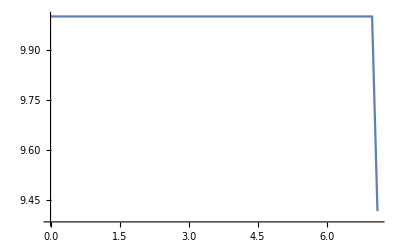

```mathematica
ListPlot[{ts, s1+i1+r1}//Transpose,Joined->True]
```